JEDNODUCHÁ GEOMETRICKÁ TRANSFORMÁCIA ŠTVORCA

==========================================

POČIATOČNÝ ŠTVOREC:

Vrcholy štvorca ABCD:

(-1 | -6
3 | -6
3 | -2
-1 | -2)

Vlastnosti štvorca:

Obsah: 16

Obvod: 16

TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE ŠTVORCA - POSUN

========================================

ZADANIE:

Majme štvorec ABCD s vrcholmi:

(-1 | -6
3 | -6
3 | -2
-1 | -2)

Vykonajte posun štvorca v 2D priestore pomocou vektora posunu: Δ = [-3, 5]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = -3

dy = 5

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre jednotlivé vrcholy:

Vrchol A:

Pôvodné súradnice: [-1, -6]

Výpočet x-ovej súradnice:

x' = x + dx = -1 + -3

x' = -4

Výpočet y-ovej súradnice:

y' = y + dy = -6 + 5

y' = -1

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4 + (3) = -1

y = y' + (-dy) = -1 + (-5) = -6

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (-1
-6
1) = (-4
-1
1)

Vrchol B:

Pôvodné súradnice: [3, -6]

Výpočet x-ovej súradnice:

x' = x + dx = 3 + -3

x' = 0

Výpočet y-ovej súradnice:

y' = y + dy = -6 + 5

y' = -1

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = 0 + (3) = 3

y = y' + (-dy) = -1 + (-5) = -6

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (3
-6
1) = (0
-1
1)

Vrchol C:

Pôvodné súradnice: [3, -2]

Výpočet x-ovej súradnice:

x' = x + dx = 3 + -3

x' = 0

Výpočet y-ovej súradnice:

y' = y + dy = -2 + 5

y' = 3

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = 0 + (3) = 3

y = y' + (-dy) = 3 + (-5) = -2

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (3
-2
1) = (0
3
1)

Vrchol D:

Pôvodné súradnice: [-1, -2]

Výpočet x-ovej súradnice:

x' = x + dx = -1 + -3

x' = -4

Výpočet y-ovej súradnice:

y' = y + dy = -2 + 5

y' = 3

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4 + (3) = -1

y = y' + (-dy) = 3 + (-5) = -2

Maticový zápis:

(1 | 0 | -3
0 | 1 | 5
0 | 0 | 1) · (-1
-2
1) = (-4
3
1)

VÝSLEDOK:

Vrcholy štvorca po posune:

(-4 | -1
0 | -1
0 | 3
-4 | 3)

VIZUALIZÁCIA:

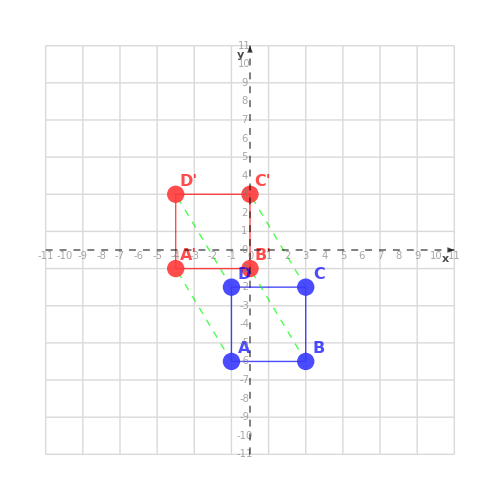

LEGENDA:

• Modré body a čiary: Pôvodný štvorec

• Červené body a čiary: Posunutý štvorec

• Zelená šípka: Vektor posunu

• Zelené prerušované čiary: Posun jednotlivých vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol A: {-1,-6}

Vrchol B: {3,-6}

Vrchol C: {3,-2}

Vrchol D: {-1,-2}

Výsledné vrcholy (červená):

Vrchol A': {-4,-1}

Vrchol B': {0,-1}

Vrchol C': {0,3}

Vrchol D': {-4,3}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [3, -5] (opačný vektor)

POSTUPNÝ VÝPOČET:

Pôvodný štvorec ABCD:

Vrcholy:

(-1 | -6
3 | -6
3 | -2
-1 | -2)

Vlastnosti štvorca:

Obsah: 16

Obvod: 16

Po transformácii (Posun):

Vrcholy štvorca A'B'C'D':

(-4 | -1
0 | -1
0 | 3
-4 | 3)

Vlastnosti štvorca:

Obsah: 16

Obvod: 16

SÚHRNNÁ VIZUALIZÁCIA:

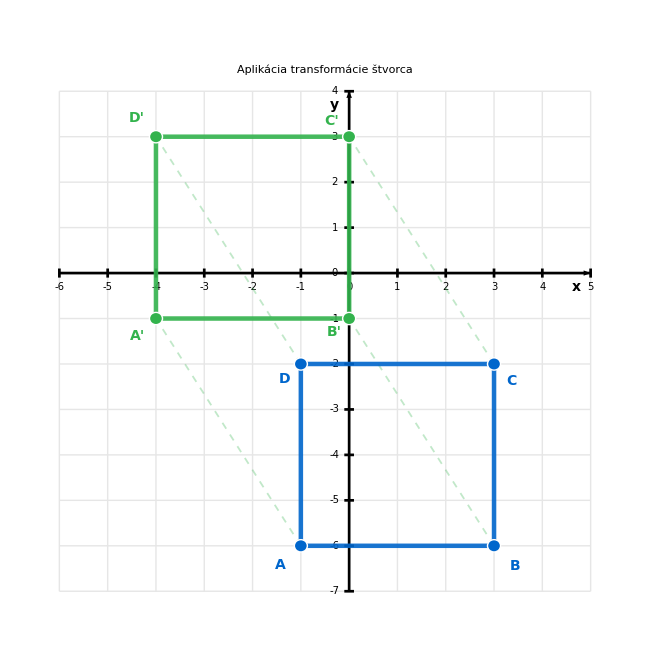

LEGENDA:

• Modré body a čiary: Pôvodný štvorec ABCD

• Tmavozelené body a čiary: Štvorec A'B'C'D' po transformácii (Posun)

Vykonaná transformácia:

Posun

{{{-1,-6},{3,-6},{3,-2},{-1,-2}},{{-4,-1},{0,-1},{0,3},{-4,3}},Posun}

```mathematica
StvorecJednoduchaTransformacia[]
```